```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=60;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

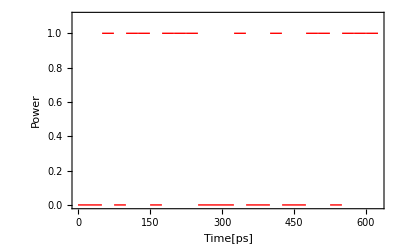

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

```mathematica
∫_0^(bit*25*10^-12) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))

```mathematica
fc[f_]:=-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))
```

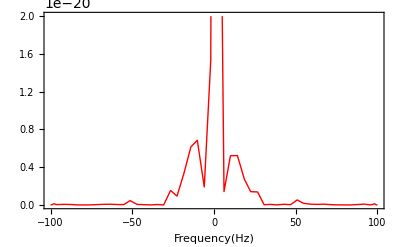

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

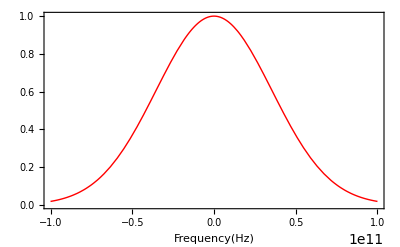

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

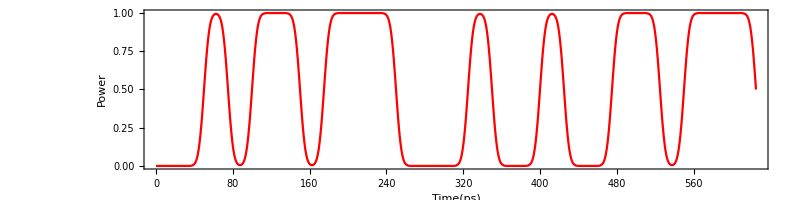

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

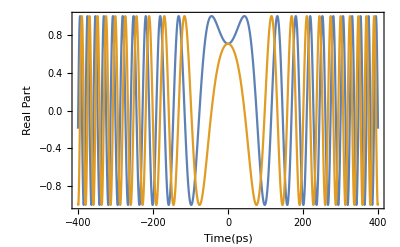

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

-22.9081+31.7428 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,39.1457},{-99.5,39.6098},{-99.,40.0263},{-98.5,40.3949},{-98.,40.7161},{-97.5,40.9912},{-97.,41.2221},{-96.5,41.4115},{-96.,41.5626},{-95.5,41.6793},{-95.,41.7659},{-94.5,41.8273},{-94.,41.8685},{-93.5,41.8948},{-93.,41.9114},{-92.5,41.9236},{-92.,41.9361},{-91.5,41.9535},{-91.,41.9798},{-90.5,42.018},{-90.,42.0708},{-89.5,42.1398},{-89.,42.2257},{-88.5,42.3284},{-88.,42.447},{-87.5,42.5799},{-87.,42.7247},{-86.5,42.8787},{-86.,43.0385},{-85.5,43.2009},{-85.,43.3625},{-84.5,43.5198},{-84.,43.67},{-83.5,43.8104},{-83.,43.9388},{-82.5,44.054},{-82.,44.1551},{-81.5,44.2421},{-81.,44.3159},{-80.5,44.378},{-80.,44.4308},{-79.5,44.4771},{-79.,44.5208},{-78.5,44.5658},{-78.,44.6167},{-77.5,44.6783},{-77.,44.7555},{-76.5,44.8529},{-76.,44.9753},{-75.5,45.1268},{-75.,45.311},{-74.5,45.5309},{-74.,45.7887},{-73.5,46.0859},{-73.,46.4228},{-72.5,46.7991},{-72.,47.2134},{-71.5,47.6635},{-71.,48.1464},{-70.5,48.6585},{-70.,49.1953},{-69.5,49.7521},{-69.,50.3235},{-68.5,50.9039},{-68.,51.4875},{-67.5,52.0681},{-67.,52.6396},{-66.5,53.1958},{-66.,53.7304},{-65.5,54.2373},{-65.,54.7103},{-64.5,55.1433},{-64.,55.5307},{-63.5,55.8665},{-63.,56.1453},{-62.5,56.3619},{-62.,56.5111},{-61.5,56.5884},{-61.,56.5894},{-60.5,56.5102},{-60.,56.3474},{-59.5,56.0983},{-59.,55.7605},{-58.5,55.3325},{-58.,54.8136},{-57.5,54.2039},{-57.,53.5042},{-56.5,52.7166},{-56.,51.844},{-55.5,50.8904},{-55.,49.8613},{-54.5,48.7629},{-54.,47.6029},{-53.5,46.3902},{-53.,45.1351},{-52.5,43.8489},{-52.,42.5442},{-51.5,41.2348},{-51.,39.9352},{-50.5,38.661},{-50.,37.428},{-49.5,36.2523},{-49.,35.1494},{-48.5,34.1343},{-48.,33.2199},{-47.5,32.4171},{-47.,31.7336},{-46.5,31.1738},{-46.,30.738},{-45.5,30.4223},{-45.,30.2191},{-44.5,30.1174},{-44.,30.1033},{-43.5,30.1613},{-43.,30.2748},{-42.5,30.4272},{-42.,30.6023},{-41.5,30.7854},{-41.,30.9631},{-40.5,31.124},{-40.,31.2589},{-39.5,31.3607},{-39.,31.4243},{-38.5,31.4469},{-38.,31.4277},{-37.5,31.368},{-37.,31.2706},{-36.5,31.1402},{-36.,30.9829},{-35.5,30.8063},{-35.,30.6188},{-34.5,30.43},{-34.,30.2499},{-33.5,30.089},{-33.,29.9576},{-32.5,29.866},{-32.,29.8238},{-31.5,29.8397},{-31.,29.921},{-30.5,30.074},{-30.,30.3031},{-29.5,30.6111},{-29.,30.9993},{-28.5,31.4674},{-28.,32.0135},{-27.5,32.6348},{-27.,33.3273},{-26.5,34.0865},{-26.,34.907},{-25.5,35.7833},{-25.,36.7096},{-24.5,37.6801},{-24.,38.6888},{-23.5,39.7299},{-23.,40.7975},{-22.5,41.8859},{-22.,42.9894},{-21.5,44.1025},{-21.,45.2195},{-20.5,46.3349},{-20.,47.4433},{-19.5,48.5393},{-19.,49.6175},{-18.5,50.6727},{-18.,51.6997},{-17.5,52.6936},{-17.,53.6493},{-16.5,54.5622},{-16.,55.4279},{-15.5,56.242},{-15.,57.0005},{-14.5,57.6998},{-14.,58.3365},{-13.5,58.9076},{-13.,59.4102},{-12.5,59.8421},{-12.,60.2014},{-11.5,60.4865},{-11.,60.6962},{-10.5,60.8298},{-10.,60.887},{-9.5,60.8681},{-9.,60.7737},{-8.5,60.605},{-8.,60.3637},{-7.5,60.0521},{-7.,59.6731},{-6.5,59.2302},{-6.,58.7277},{-5.5,58.1706},{-5.,57.5646},{-4.5,56.9161},{-4.,56.2324},{-3.5,55.5215},{-3.,54.7922},{-2.5,54.0539},{-2.,53.3164},{-1.5,52.59},{-1.,51.8853},{-0.5,51.2127},{0.,50.5821},{0.5,50.0029},{1.,49.4833},{1.5,49.0302},{2.,48.6484},{2.5,48.341},{3.,48.1085},{3.5,47.949},{4.,47.8582},{4.5,47.8292},{5.,47.8531},{5.5,47.919},{6.,48.0146},{6.5,48.1265},{7.,48.2404},{7.5,48.3421},{8.,48.4173},{8.5,48.4524},{9.,48.4347},{9.5,48.3525},{10.,48.1957},{10.5,47.9556},{11.,47.6255},{11.5,47.2003},{12.,46.6769},{12.5,46.0543},{13.,45.3333},{13.5,44.5168},{14.,43.6097},{14.5,42.6186},{15.,41.552},{15.5,40.42},{16.,39.2343},{16.5,38.0078},{17.,36.7545},{17.5,35.4891},{18.,34.227},{18.5,32.9832},{19.,31.7726},{19.5,30.6088},{20.,29.504},{20.5,28.4681},{21.,27.5084},{21.5,26.6287},{22.,25.8296},{22.5,25.108},{23.,24.4574},{23.5,23.8683},{24.,23.329},{24.5,22.8266},{25.,22.3474},{25.5,21.8784},{26.,21.4076},{26.5,20.9253},{27.,20.4245},{27.5,19.9014},{28.,19.356},{28.5,18.7924},{29.,18.2196},{29.5,17.6514},{30.,17.1068},{30.5,16.6101},{31.,16.1905},{31.5,15.8803},{32.,15.713},{32.5,15.7199},{33.,15.9261},{33.5,16.347},{34.,16.9869},{34.5,17.8394},{35.,18.8899},{35.5,20.1189},{36.,21.5047},{36.5,23.026},{37.,24.6632},{37.5,26.399},{38.,28.2185},{38.5,30.1095},{39.,32.0618},{39.5,34.0672},{40.,36.1187},{40.5,38.2109},{41.,40.3388},{41.5,42.4981},{42.,44.6849},{42.5,46.8951},{43.,49.1246},{43.5,51.3689},{44.,53.623},{44.5,55.8815},{45.,58.1383},{45.5,60.3871},{46.,62.6208},{46.5,64.832},{47.,67.0131},{47.5,69.1564},{48.,71.2542},{48.5,73.2989},{49.,75.2837},{49.5,77.2018},{50.,79.0478},{50.5,80.8167},{51.,82.505},{51.5,84.1103},{52.,85.6312},{52.5,87.0682},{53.,88.423},{53.5,89.6985},{54.,90.8992},{54.5,92.0309},{55.,93.1003},{55.5,94.1152},{56.,95.084},{56.5,96.0156},{57.,96.9191},{57.5,97.8031},{58.,98.6762},{58.5,99.5458},{59.,100.418},{59.5,101.299},{60.,102.191},{60.5,103.097},{61.,104.015},{61.5,104.945},{62.,105.883},{62.5,106.823},{63.,107.758},{63.5,108.68},{64.,109.581},{64.5,110.45},{65.,111.277},{65.5,112.052},{66.,112.764},{66.5,113.406},{67.,113.967},{67.5,114.441},{68.,114.821},{68.5,115.103},{69.,115.285},{69.5,115.364},{70.,115.343},{70.5,115.223},{71.,115.01},{71.5,114.711},{72.,114.334},{72.5,113.891},{73.,113.393},{73.5,112.855},{74.,112.291},{74.5,111.718},{75.,111.153},{75.5,110.613},{76.,110.116},{76.5,109.678},{77.,109.316},{77.5,109.044},{78.,108.874},{78.5,108.817},{79.,108.881},{79.5,109.07},{80.,109.386},{80.5,109.826},{81.,110.385},{81.5,111.055},{82.,111.824},{82.5,112.678},{83.,113.601},{83.5,114.574},{84.,115.577},{84.5,116.59},{85.,117.592},{85.5,118.561},{86.,119.478},{86.5,120.323},{87.,121.077},{87.5,121.723},{88.,122.249},{88.5,122.64},{89.,122.889},{89.5,122.988},{90.,122.933},{90.5,122.726},{91.,122.367},{91.5,121.866},{92.,121.231},{92.5,120.478},{93.,119.623},{93.5,118.687},{94.,117.694},{94.5,116.671},{95.,115.646},{95.5,114.649},{96.,113.709},{96.5,112.858},{97.,112.123},{97.5,111.528},{98.,111.097},{98.5,110.843},{99.,110.779},{99.5,110.908},{100.,111.226},{100.5,111.725},{101.,112.387},{101.5,113.192},{102.,114.114},{102.5,115.123},{103.,116.187},{103.5,117.274},{104.,118.352},{104.5,119.39},{105.,120.358},{105.5,121.231},{106.,121.987},{106.5,122.606},{107.,123.076},{107.5,123.387},{108.,123.535},{108.5,123.52},{109.,123.348},{109.5,123.028},{110.,122.575},{110.5,122.006},{111.,121.344},{111.5,120.613},{112.,119.837},{112.5,119.045},{113.,118.263},{113.5,117.517},{114.,116.831},{114.5,116.225},{115.,115.716},{115.5,115.315},{116.,115.027},{116.5,114.851},{117.,114.781},{117.5,114.804},{118.,114.902},{118.5,115.054},{119.,115.233},{119.5,115.411},{120.,115.558},{120.5,115.645},{121.,115.642},{121.5,115.522},{122.,115.259},{122.5,114.832},{123.,114.222},{123.5,113.414},{124.,112.399},{124.5,111.171},{125.,109.73},{125.5,108.08},{126.,106.231},{126.5,104.196},{127.,101.995},{127.5,99.6522},{128.,97.196},{128.5,94.6598},{129.,92.081},{129.5,89.501},{130.,86.9641},{130.5,84.5175},{131.,82.2093},{131.5,80.0881},{132.,78.2002},{132.5,76.5886},{133.,75.2899},{133.5,74.3328},{134.,73.7357},{134.5,73.5061},{135.,73.6399},{135.5,74.1222},{136.,74.9289},{136.5,76.0291},{137.,77.3871},{137.5,78.9652},{138.,80.7257},{138.5,82.6325},{139.,84.6523},{139.5,86.7556},{140.,88.9165},{140.5,91.1134},{141.,93.3283},{141.5,95.5472},{142.,97.759},{142.5,99.9555},{143.,102.131},{143.5,104.282},{144.,106.405},{144.5,108.5},{145.,110.566},{145.5,112.604},{146.,114.613},{146.5,116.595},{147.,118.549},{147.5,120.475},{148.,122.373},{148.5,124.243},{149.,126.083},{149.5,127.892},{150.,129.668},{150.5,131.409},{151.,133.114},{151.5,134.779},{152.,136.403},{152.5,137.984},{153.,139.52},{153.5,141.009},{154.,142.45},{154.5,143.841},{155.,145.182},{155.5,146.472},{156.,147.71},{156.5,148.897},{157.,150.033},{157.5,151.119},{158.,152.154},{158.5,153.139},{159.,154.076},{159.5,154.964},{160.,155.806},{160.5,156.6},{161.,157.347},{161.5,158.048},{162.,158.702},{162.5,159.309},{163.,159.868},{163.5,160.379},{164.,160.839},{164.5,161.247},{165.,161.602},{165.5,161.902},{166.,162.145},{166.5,162.33},{167.,162.454},{167.5,162.518},{168.,162.519},{168.5,162.46},{169.,162.34},{169.5,162.161},{170.,161.928},{170.5,161.643},{171.,161.313},{171.5,160.947},{172.,160.551},{172.5,160.138},{173.,159.72},{173.5,159.31},{174.,158.923},{174.5,158.576},{175.,158.285},{175.5,158.068},{176.,157.943},{176.5,157.925},{177.,158.031},{177.5,158.276},{178.,158.672},{178.5,159.227},{179.,159.95},{179.5,160.843},{180.,161.906},{180.5,163.136},{181.,164.525},{181.5,166.063},{182.,167.736},{182.5,169.527},{183.,171.418},{183.5,173.388},{184.,175.416},{184.5,177.48},{185.,179.556},{185.5,181.623},{186.,183.659},{186.5,185.643},{187.,187.556},{187.5,189.38},{188.,191.1},{188.5,192.7},{189.,194.168},{189.5,195.493},{190.,196.667},{190.5,197.681},{191.,198.53},{191.5,199.208},{192.,199.712},{192.5,200.04},{193.,200.188},{193.5,200.155},{194.,199.94},{194.5,199.541},{195.,198.957},{195.5,198.186},{196.,197.227},{196.5,196.078},{197.,194.736},{197.5,193.201},{198.,191.469},{198.5,189.539},{199.,187.41},{199.5,185.081},{200.,182.551},{200.5,179.822},{201.,176.895},{201.5,173.775},{202.,170.466},{202.5,166.976},{203.,163.314},{203.5,159.492},{204.,155.522},{204.5,151.422},{205.,147.21},{205.5,142.907},{206.,138.535},{206.5,134.121},{207.,129.691},{207.5,125.275},{208.,120.904},{208.5,116.609},{209.,112.423},{209.5,108.379},{210.,104.51},{210.5,100.848},{211.,97.4231},{211.5,94.2635},{212.,91.3947},{212.5,88.8385},{213.,86.6126},{213.5,84.7301},{214.,83.1995},{214.5,82.0246},{215.,81.2051},{215.5,80.7368},{216.,80.6124},{216.5,80.8226},{217.,81.3565},{217.5,82.2024},{218.,83.3482},{218.5,84.7817},{219.,86.4902},{219.5,88.461},{220.,90.6807},{220.5,93.1346},{221.,95.8071},{221.5,98.6808},{222.,101.736},{222.5,104.953},{223.,108.307},{223.5,111.774},{224.,115.327},{224.5,118.939},{225.,122.581},{225.5,126.224},{226.,129.838},{226.5,133.394},{227.,136.864},{227.5,140.219},{228.,143.434},{228.5,146.484},{229.,149.346},{229.5,151.999},{230.,154.425},{230.5,156.607},{231.,158.533},{231.5,160.192},{232.,161.574},{232.5,162.673},{233.,163.487},{233.5,164.013},{234.,164.252},{234.5,164.206},{235.,163.879},{235.5,163.278},{236.,162.408},{236.5,161.278},{237.,159.895},{237.5,158.27},{238.,156.411},{238.5,154.328},{239.,152.033},{239.5,149.534},{240.,146.843},{240.5,143.97},{241.,140.928},{241.5,137.728},{242.,134.384},{242.5,130.911},{243.,127.324},{243.5,123.644},{244.,119.89},{244.5,116.089},{245.,112.268},{245.5,108.462},{246.,104.707},{246.5,101.049},{247.,97.5363},{247.5,94.2233},{248.,91.1697},{248.5,88.4378},{249.,86.091},{249.5,84.1902},{250.,82.7892},{250.5,81.9306},{251.,81.6413},{251.5,81.9292},{252.,82.7824},{252.5,84.1698},{253.,86.0445},{253.5,88.3475},{254.,91.0127},{254.5,93.9709},{255.,97.1534},{255.5,100.494},{256.,103.933},{256.5,107.413},{257.,110.885},{257.5,114.305},{258.,117.636},{258.5,120.846},{259.,123.907},{259.5,126.799},{260.,129.505},{260.5,132.01},{261.,134.308},{261.5,136.391},{262.,138.259},{262.5,139.913},{263.,141.354},{263.5,142.59},{264.,143.627},{264.5,144.476},{265.,145.145},{265.5,145.646},{266.,145.992},{266.5,146.194},{267.,146.265},{267.5,146.217},{268.,146.062},{268.5,145.812},{269.,145.477},{269.5,145.069},{270.,144.595},{270.5,144.065},{271.,143.487},{271.5,142.866},{272.,142.209},{272.5,141.521},{273.,140.805},{273.5,140.065},{274.,139.303},{274.5,138.521},{275.,137.72},{275.5,136.899},{276.,136.058},{276.5,135.195},{277.,134.308},{277.5,133.393},{278.,132.447},{278.5,131.466},{279.,130.443},{279.5,129.374},{280.,128.252},{280.5,127.07},{281.,125.821},{281.5,124.497},{282.,123.091},{282.5,121.595},{283.,120.002},{283.5,118.305},{284.,116.498},{284.5,114.574},{285.,112.529},{285.5,110.359},{286.,108.06},{286.5,105.63},{287.,103.068},{287.5,100.376},{288.,97.5533},{288.5,94.604},{289.,91.5318},{289.5,88.3421},{290.,85.0413},{290.5,81.637},{291.,78.1381},{291.5,74.5544},{292.,70.897},{292.5,67.1781},{293.,63.4111},{293.5,59.6109},{294.,55.7941},{294.5,51.9792},{295.,48.1877},{295.5,44.4448},{296.,40.7806},{296.5,37.2325},{297.,33.8475},{297.5,30.6861},{298.,27.8257},{298.5,25.3634},{299.,23.4131},{299.5,22.0911},{300.,21.4865},{300.5,21.6256},{301.,22.4557},{301.5,23.8623},{302.,25.7058},{302.5,27.8533},{303.,30.1927},{303.5,32.6353},{304.,35.1121},{304.5,37.5693},{305.,39.9642},{305.5,42.2621},{306.,44.4341},{306.5,46.4557},{307.,48.3056},{307.5,49.9653},{308.,51.4184},{308.5,52.6506},{309.,53.6495},{309.5,54.4045},{310.,54.9068},{310.5,55.1494},{311.,55.1273},{311.5,54.8375},{312.,54.2789},{312.5,53.4526},{313.,52.3622},{313.5,51.0132},{314.,49.4139},{314.5,47.575},{315.,45.5101},{315.5,43.2358},{316.,40.7722},{316.5,38.1435},{317.,35.3789},{317.5,32.5144},{318.,29.5948},{318.5,26.6782},{319.,23.8417},{319.5,21.1912},{320.,18.8718},{320.5,17.073},{321.,16.0065},{321.5,15.8327},{322.,16.5681},{322.5,18.0709},{323.,20.125},{323.5,22.525},{324.,25.111},{324.5,27.7667},{325.,30.4084},{325.5,32.9743},{326.,35.4178},{326.5,37.7024},{327.,39.7989},{327.5,41.6839},{328.,43.3382},{328.5,44.7463},{329.,45.896},{329.5,46.7783},{330.,47.3865},{330.5,47.7169},{331.,47.7683},{331.5,47.5419},{332.,47.0418},{332.5,46.2743},{333.,45.2487},{333.5,43.9771},{334.,42.4747},{334.5,40.7602},{335.,38.8562},{335.5,36.7905},{336.,34.5965},{336.5,32.3159},{337.,30.0004},{337.5,27.7158},{338.,25.5461},{338.5,23.5974},{339.,21.9986},{339.5,20.8922},{340.,20.4087},{340.5,20.6278},{341.,21.5486},{341.5,23.094},{342.,25.1442},{342.5,27.5731},{343.,30.2695},{343.5,33.1438},{344.,36.1269},{344.5,39.1663},{345.,42.2227},{345.5,45.2672},{346.,48.2786},{346.5,51.2422},{347.,54.1486},{347.5,56.9931},{348.,59.7746},{348.5,62.4956},{349.,65.1612},{349.5,67.7789},{350.,70.3581},{350.5,72.9095},{351.,75.4446},{351.5,77.9751},{352.,80.5124},{352.5,83.0669},{353.,85.6477},{353.5,88.2621},{354.,90.9149},{354.5,93.6084},{355.,96.3424},{355.5,99.1134},{356.,101.915},{356.5,104.739},{357.,107.574},{357.5,110.406},{358.,113.22},{358.5,115.998},{359.,118.723},{359.5,121.375},{360.,123.935},{360.5,126.384},{361.,128.703},{361.5,130.875},{362.,132.882},{362.5,134.71},{363.,136.343},{363.5,137.77},{364.,138.981},{364.5,139.969},{365.,140.726},{365.5,141.251},{366.,141.542},{366.5,141.6},{367.,141.43},{367.5,141.036},{368.,140.427},{368.5,139.613},{369.,138.606},{369.5,137.42},{370.,136.069},{370.5,134.571},{371.,132.942},{371.5,131.201},{372.,129.367},{372.5,127.459},{373.,125.495},{373.5,123.495},{374.,121.476},{374.5,119.454},{375.,117.446},{375.5,115.465},{376.,113.523},{376.5,111.632},{377.,109.799},{377.5,108.03},{378.,106.329},{378.5,104.697},{379.,103.135},{379.5,101.638},{380.,100.203},{380.5,98.8249},{381.,97.4949},{381.5,96.2053},{382.,94.9469},{382.5,93.7103},{383.,92.4857},{383.5,91.2633},{384.,90.0339},{384.5,88.7883},{385.,87.5184},{385.5,86.2163},{386.,84.8755},{386.5,83.49},{387.,82.0549},{387.5,80.5662},{388.,79.0208},{388.5,77.4164},{389.,75.7518},{389.5,74.0263},{390.,72.24},{390.5,70.3935},{391.,68.4881},{391.5,66.5252},{392.,64.5068},{392.5,62.4346},{393.,60.311},{393.5,58.1377},{394.,55.9167},{394.5,53.6496},{395.,51.3377},{395.5,48.9821},{396.,46.5832},{396.5,44.1412},{397.,41.656},{397.5,39.1269},{398.,36.5529},{398.5,33.933},{399.,31.2657},{399.5,28.5497},{400.,25.7837},{400.5,22.9666},{401.,20.0977},{401.5,17.1769},{402.,14.2046},{402.5,11.1822},{403.,8.11246},{403.5,5.00152},{404.,1.87987},{404.5,1.47271},{405.,4.64808},{405.5,7.89782},{406.,11.1729},{406.5,14.4609},{407.,17.752},{407.5,21.0362},{408.,24.3037},{408.5,27.5441},{409.,30.7473},{409.5,33.9032},{410.,37.0018},{410.5,40.0339},{411.,42.9905},{411.5,45.8639},{412.,48.6469},{412.5,51.3338},{413.,53.9199},{413.5,56.4019},{414.,58.7777},{414.5,61.0467},{415.,63.2099},{415.5,65.2692},{416.,67.2279},{416.5,69.0903},{417.,70.8616},{417.5,72.5475},{418.,74.1541},{418.5,75.6877},{419.,77.154},{419.5,78.5585},{420.,79.9056},{420.5,81.1986},{421.,82.4397},{421.5,83.6292},{422.,84.766},{422.5,85.8473},{423.,86.8686},{423.5,87.8237},{424.,88.7052},{424.5,89.5044},{425.,90.2119},{425.5,90.8176},{426.,91.3111},{426.5,91.6823},{427.,91.9216},{427.5,92.0204},{428.,91.9712},{428.5,91.7686},{429.,91.4087},{429.5,90.8905},{430.,90.2153},{430.5,89.3874},{431.,88.4146},{431.5,87.3078},{432.,86.0817},{432.5,84.7548},{433.,83.3493},{433.5,81.8914},{434.,80.4108},{434.5,78.9408},{435.,77.5177},{435.5,76.1799},{436.,74.9673},{436.5,73.9197},{437.,73.0753},{437.5,72.4691},{438.,72.1308},{438.5,72.0832},{439.,72.3406},{439.5,72.9086},{440.,73.7833},{440.5,74.9523},{441.,76.3957},{441.5,78.0879},{442.,79.999},{442.5,82.0971},{443.,84.3493},{443.5,86.7233},{444.,89.1882},{444.5,91.7153},{445.,94.2787},{445.5,96.8549},{446.,99.4239},{446.5,101.968},{447.,104.473},{447.5,106.927},{448.,109.32},{448.5,111.645},{449.,113.896},{449.5,116.07},{450.,118.165},{450.5,120.18},{451.,122.114},{451.5,123.969},{452.,125.746},{452.5,127.446},{453.,129.072},{453.5,130.625},{454.,132.108},{454.5,133.522},{455.,134.868},{455.5,136.148},{456.,137.362},{456.5,138.509},{457.,139.59},{457.5,140.603},{458.,141.547},{458.5,142.419},{459.,143.217},{459.5,143.937},{460.,144.577},{460.5,145.132},{461.,145.598},{461.5,145.971},{462.,146.247},{462.5,146.421},{463.,146.489},{463.5,146.448},{464.,146.293},{464.5,146.023},{465.,145.635},{465.5,145.128},{466.,144.5},{466.5,143.752},{467.,142.885},{467.5,141.903},{468.,140.807},{468.5,139.603},{469.,138.295},{469.5,136.892},{470.,135.4},{470.5,133.828},{471.,132.185},{471.5,130.48},{472.,128.722},{472.5,126.923},{473.,125.091},{473.5,123.236},{474.,121.365},{474.5,119.487},{475.,117.607},{475.5,115.73},{476.,113.858},{476.5,111.993},{477.,110.134},{477.5,108.278},{478.,106.422},{478.5,104.559},{479.,102.684},{479.5,100.786},{480.,98.8584},{480.5,96.891},{481.,94.8747},{481.5,92.8008},{482.,90.6609},{482.5,88.448},{483.,86.1563},{483.5,83.7817},{484.,81.3217},{484.5,78.7761},{485.,76.1468},{485.5,73.4377},{486.,70.6552},{486.5,67.808},{487.,64.9068},{487.5,61.9647},{488.,58.997},{488.5,56.0207},{489.,53.0548},{489.5,50.1202},{490.,47.239},{490.5,44.435},{491.,41.7329},{491.5,39.158},{492.,36.7359},{492.5,34.4916},{493.,32.4486},{493.5,30.6273},{494.,29.0441},{494.5,27.7089},{495.,26.6241},{495.5,25.7838},{496.,25.1736},{496.5,24.7721},{497.,24.5527},{497.5,24.487},{498.,24.5468},{498.5,24.7071},{499.,24.9469},{499.5,25.251},{500.,25.6094},{500.5,26.0181},{501.,26.4779},{501.5,26.9941},{502.,27.5757},{502.5,28.2346},{503.,28.9843},{503.5,29.8395},{504.,30.8149},{504.5,31.9242},{505.,33.1798},{505.5,34.592},{506.,36.1688},{506.5,37.9154},{507.,39.8346},{507.5,41.9267},{508.,44.1895},{508.5,46.6188},{509.,49.2081},{509.5,51.9493},{510.,54.8323},{510.5,57.8458},{511.,60.9767},{511.5,64.2106},{512.,67.5319},{512.5,70.9236},{513.,74.3681},{513.5,77.8467},{514.,81.34},{514.5,84.8283},{515.,88.2919},{515.5,91.711},{516.,95.0664},{516.5,98.3397},{517.,101.514},{517.5,104.572},{518.,107.502},{518.5,110.292},{519.,112.932},{519.5,115.417},{520.,117.743},{520.5,119.912},{521.,121.927},{521.5,123.797},{522.,125.534},{522.5,127.152},{523.,128.671},{523.5,130.112},{524.,131.5},{524.5,132.86},{525.,134.221},{525.5,135.609},{526.,137.052},{526.5,138.573},{527.,140.196},{527.5,141.938},{528.,143.812},{528.5,145.828},{529.,147.986},{529.5,150.285},{530.,152.716},{530.5,155.264},{531.,157.911},{531.5,160.635},{532.,163.412},{532.5,166.214},{533.,169.015},{533.5,171.788},{534.,174.507},{534.5,177.148},{535.,179.691},{535.5,182.117},{536.,184.416},{536.5,186.576},{537.,188.594},{537.5,190.47},{538.,192.21},{538.5,193.823},{539.,195.322},{539.5,196.724},{540.,198.049},{540.5,199.32},{541.,200.559},{541.5,201.79},{542.,203.034},{542.5,204.313},{543.,205.644},{543.5,207.04},{544.,208.51},{544.5,210.058},{545.,211.681},{545.5,213.372},{546.,215.115},{546.5,216.892},{547.,218.68},{547.5,220.448},{548.,222.167},{548.5,223.801},{549.,225.315},{549.5,226.674},{550.,227.842},{550.5,228.785},{551.,229.472},{551.5,229.873},{552.,229.964},{552.5,229.723},{553.,229.133},{553.5,228.182},{554.,226.863},{554.5,225.174},{555.,223.117},{555.5,220.701},{556.,217.937},{556.5,214.844},{557.,211.442},{557.5,207.756},{558.,203.816},{558.5,199.652},{559.,195.299},{559.5,190.792},{560.,186.169},{560.5,181.467},{561.,176.724},{561.5,171.977},{562.,167.261},{562.5,162.609},{563.,158.053},{563.5,153.619},{564.,149.333},{564.5,145.214},{565.,141.278},{565.5,137.538},{566.,134.002},{566.5,130.674},{567.,127.556},{567.5,124.646},{568.,121.941},{568.5,119.436},{569.,117.126},{569.5,115.004},{570.,113.065},{570.5,111.305},{571.,109.72},{571.5,108.306},{572.,107.063},{572.5,105.989},{573.,105.083},{573.5,104.346},{574.,103.775},{574.5,103.369},{575.,103.125},{575.5,103.038},{576.,103.102},{576.5,103.308},{577.,103.647},{577.5,104.108},{578.,104.678},{578.5,105.343},{579.,106.091},{579.5,106.908},{580.,107.78},{580.5,108.695},{581.,109.643},{581.5,110.612},{582.,111.593},{582.5,112.581},{583.,113.567},{583.5,114.547},{584.,115.517},{584.5,116.474},{585.,117.412},{585.5,118.33},{586.,119.223},{586.5,120.087},{587.,120.917},{587.5,121.707},{588.,122.448},{588.5,123.134},{589.,123.754},{589.5,124.298},{590.,124.755},{590.5,125.113},{591.,125.361},{591.5,125.488},{592.,125.482},{592.5,125.335},{593.,125.038},{593.5,124.586},{594.,123.975},{594.5,123.205},{595.,122.278},{595.5,121.201},{596.,119.983},{596.5,118.637},{597.,117.182},{597.5,115.639},{598.,114.034},{598.5,112.394},{599.,110.753},{599.5,109.144},{600.,107.605},{600.5,106.171},{601.,104.88},{601.5,103.765},{602.,102.858},{602.5,102.184},{603.,101.763},{603.5,101.608},{604.,101.724},{604.5,102.106},{605.,102.743},{605.5,103.617},{606.,104.702},{606.5,105.971},{607.,107.392},{607.5,108.93},{608.,110.554},{608.5,112.23},{609.,113.929},{609.5,115.622},{610.,117.287},{610.5,118.902},{611.,120.451},{611.5,121.922},{612.,123.305},{612.5,124.596},{613.,125.792},{613.5,126.895},{614.,127.909},{614.5,128.839},{615.,129.692},{615.5,130.478},{616.,131.206},{616.5,131.885},{617.,132.525},{617.5,133.133},{618.,133.718},{618.5,134.285},{619.,134.838},{619.5,135.379},{620.,135.909},{620.5,136.426},{621.,136.925},{621.5,137.402},{622.,137.851},{622.5,138.262},{623.,138.628},{623.5,138.938},{624.,139.184},{624.5,139.357},{625.,139.446},{625.5,139.446},{626.,139.347},{626.5,139.146},{627.,138.837},{627.5,138.418},{628.,137.888},{628.5,137.247},{629.,136.498},{629.5,135.645},{630.,134.692},{630.5,133.646},{631.,132.515},{631.5,131.308},{632.,130.034},{632.5,128.704},{633.,127.326},{633.5,125.912},{634.,124.471},{634.5,123.011},{635.,121.542},{635.5,120.071},{636.,118.602},{636.5,117.142},{637.,115.692},{637.5,114.254},{638.,112.827},{638.5,111.41},{639.,109.999},{639.5,108.589},{640.,107.175},{640.5,105.751},{641.,104.308},{641.5,102.84},{642.,101.34},{642.5,99.7998},{643.,98.2137},{643.5,96.5762},{644.,94.8831},{644.5,93.1314},{645.,91.3201},{645.5,89.4498},{646.,87.5231},{646.5,85.545},{647.,83.5223},{647.5,81.4645},{648.,79.3829},{648.5,77.2916},{649.,75.2062},{649.5,73.1449},{650.,71.127},{650.5,69.1735},{651.,67.306},{651.5,65.5463},{652.,63.9157},{652.5,62.4338},{653.,61.1178},{653.5,59.9813},{654.,59.0336},{654.5,58.2787},{655.,57.7149},{655.5,57.3348},{656.,57.1254},{656.5,57.0688},{657.,57.1431},{657.5,57.3237},{658.,57.5838},{658.5,57.8964},{659.,58.2346},{659.5,58.5728},{660.,58.8871},{660.5,59.1559},{661.,59.3603},{661.5,59.4843},{662.,59.5147},{662.5,59.4414},{663.,59.2573},{663.5,58.9579},{664.,58.5417},{664.5,58.0097},{665.,57.3655},{665.5,56.6147},{666.,55.7652},{666.5,54.8267},{667.,53.8105},{667.5,52.7291},{668.,51.5964},{668.5,50.4267},{669.,49.2348},{669.5,48.0356},{670.,46.8436},{670.5,45.6723},{671.,44.5342},{671.5,43.4402},{672.,42.399},{672.5,41.4171},{673.,40.4983},{673.5,39.6439},{674.,38.8522},{674.5,38.1193},{675.,37.4387},{675.5,36.8022},{676.,36.1999},{676.5,35.621},{677.,35.0543},{677.5,34.4885},{678.,33.9126},{678.5,33.3166},{679.,32.6914},{679.5,32.029},{680.,31.3229},{680.5,30.5681},{681.,29.7609},{681.5,28.8989},{682.,27.9813},{682.5,27.0081},{683.,25.9808},{683.5,24.9014},{684.,23.773},{684.5,22.5992},{685.,21.3842},{685.5,20.1323},{686.,18.8482},{686.5,17.5367},{687.,16.2023},{687.5,14.8495},{688.,13.4827},{688.5,12.1057},{689.,10.722},{689.5,9.33489},{690.,7.94699},{690.5,6.56059},{691.,5.17753},{691.5,3.79926},{692.,2.42687},{692.5,1.06119},{693.,0.297751},{693.5,1.6485},{694.,2.99173},{694.5,4.32709},{695.,5.65445},{695.5,6.97364},{696.,8.28443},{696.5,9.58648},{697.,10.8793},{697.5,12.1624},{698.,13.4349},{698.5,14.696},{699.,15.9446},{699.5,17.1798},{700.,18.4003},{700.5,19.6048},{701.,20.7922},{701.5,21.9611},{702.,23.1103},{702.5,24.2386},{703.,25.3448},{703.5,26.4277},{704.,27.4862},{704.5,28.5195},{705.,29.5264},{705.5,30.5061},{706.,31.4577},{706.5,32.3804},{707.,33.2733},{707.5,34.1356},{708.,34.9665},{708.5,35.7651},{709.,36.5307},{709.5,37.2625},{710.,37.9597},{710.5,38.6215},{711.,39.2472},{711.5,39.8362},{712.,40.388},{712.5,40.9021},{713.,41.3783},{713.5,41.8164},{714.,42.2166},{714.5,42.579},{715.,42.9043},{715.5,43.1932},{716.,43.4466},{716.5,43.6658},{717.,43.8522},{717.5,44.0074},{718.,44.1332},{718.5,44.2316},{719.,44.3045},{719.5,44.3541},{720.,44.3825},{720.5,44.3917},{721.,44.3837},{721.5,44.3604},{722.,44.3235},{722.5,44.2745},{723.,44.2146},{723.5,44.1451},{724.,44.0666},{724.5,43.9799},{725.,43.8854}}

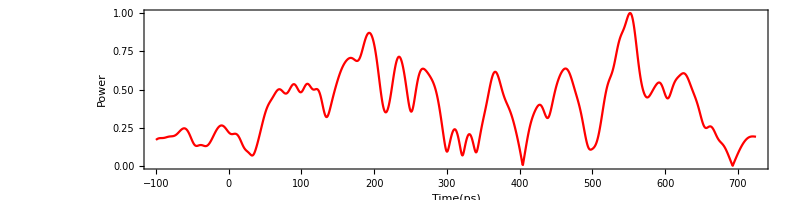

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

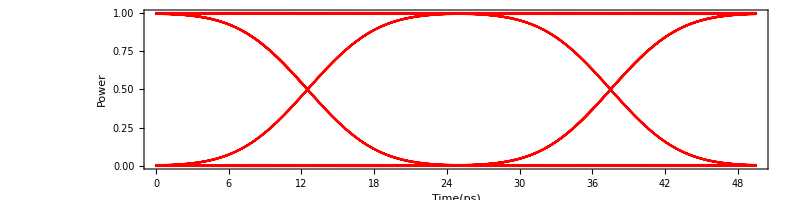

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

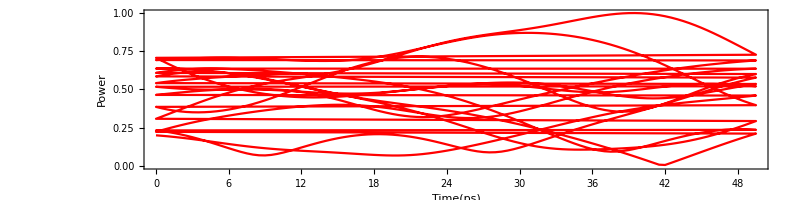

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 55 point

0 is 77 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.676961

Average of 0 is 0.280035

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.13384

A Standard Deviation of 0 is 0.114129

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

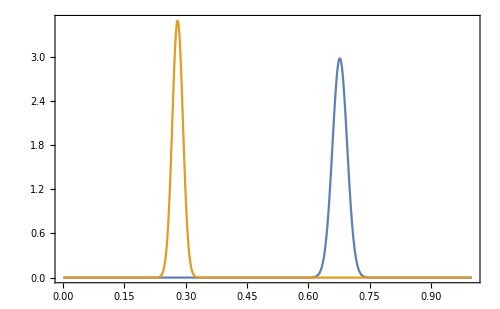

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 1.60071

Q-dB is 4.08626 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.0547204

Eye Opening is 0.375278

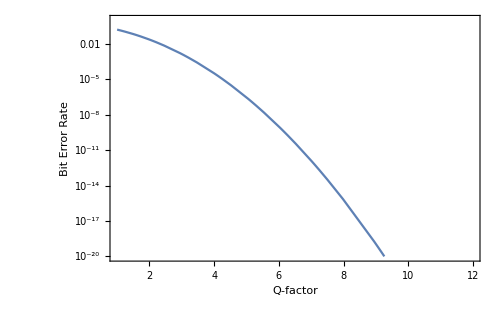

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```